```mathematica
TransformedDistribution[
σScreen*σScreen,
{
σScreen\[Distributed]NormalDistribution[μσScreen,σσScreen],
σOff\[Distributed]NormalDistribution[μσOff,σσOff]
}
]
```

TransformedDistribution[x1^2,{x1}\[Distributed]TransformedDistribution[{x},x\[Distributed]NormalDistribution[μσScreen,σσScreen]]]

```mathematica
data =ImportString[" -1, 0.001463870524947474
 0, 0.00047288595738029726
 1, 0.0015314520018408838
 -1, 0.0015990216946601093
 0, 0.000488025717938945
 1, 0.001702715083358308
 -1, 0.0015840824570475
 0, 0.0004415050596621244
 1, 0.0016658283063040557
 -1, 0.001981712299712555
 0, 0.0005222530245381091
 1, 0.0017697200301395532
 -1, 0.0014666899862966108
 0, 0.00045537560463279814
 1, 0.0018473205035243142
 -1, 0.0013760208707809464
 0, 0.0004859513693057428
 1, 0.00173260856250911
 -1, 0.002051708016449268
 0, 0.0004954909340642246
 1, 0.0010361132520943922
 -1, 0.0019271012186153709
 0, 0.0004533206230957517
 1, 0.001938710604969935
 -1, 0.0017277901577373476
 0, 0.00048823842599653476
 1, 0.0015677181790459992
 -1, 0.0017144755734529442
 0, 0.0004857739148630236
 1, 0.001810528644912713
","CSV"];

(*data=data[[1;;6]];*)

(*Convert to microns*)
data[[All,2]]*=10^6;
```

```mathematica
exprσScreen = √(σOff^2+(κ V σz)^2)/.κ->(1/0.073);
nlm = NonlinearModelFit[
data,
exprσScreen,
{σOff,σz},
V
]
```

FittedModel[…]

```mathematica
aroundData = Around[#[[All,2]]]&/@GroupBy[data,First]
```

<|-1→1689.234.,0→479.24.,1→1660.251.|>

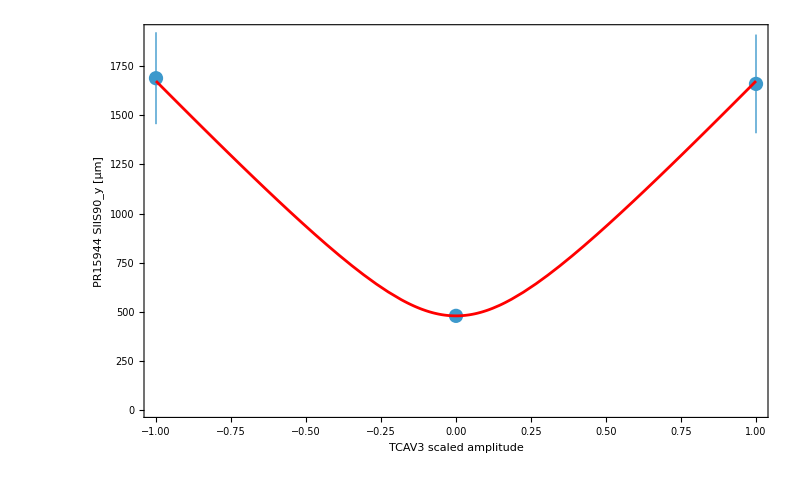

```mathematica
Show[
ListPlot[aroundData,ImageSize->800,Frame->True,LabelStyle->20,FrameLabel->{"TCAV3 scaled amplitude", "PR15944 SIIS90_y [μm]"}],
Plot[nlm["BestFit"],{V,-1,1},PlotStyle->Red]
]
```

```mathematica
nlm["ParameterEstimates"]
```

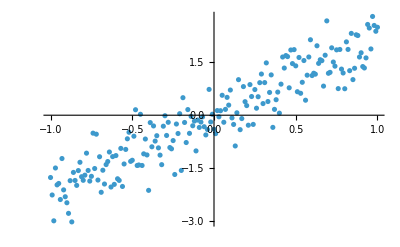

```mathematica
fakeData = Table[{x, 2.1 x + 0.5RandomVariate[NormalDistribution[0,1],1][[1]]},{x,-1,1,0.01}];

(*Randomize order*)
fakeData=RandomSample[fakeData];


ListPlot[fakeData]
```

```mathematica
nlm = NonlinearModelFit[
fakeData[[1;;20]],
m x + b,
{m,b},
x
];
nlm["ParameterEstimates"]
```

```mathematica
nlm = NonlinearModelFit[
fakeData[[1;;50]],
m x + b,
{m,b},
x
];
nlm["ParameterEstimates"]
```

```mathematica
nlm = NonlinearModelFit[
fakeData[[1;;100]],
m x + b,
{m,b},
x
];
nlm["ParameterEstimates"]
```